```mathematica
Norm[{1,2,3}]
```

√14

```mathematica
Norm[{x,y,z}]
```

√(x^2+y^2+z^2)

```mathematica
f[theta_,phi_]={Sin[phi]Cos[theta],Sin[phi]Sin[theta],Cos[phi]};
ParametricPlot3D[f[theta,phi],{theta,0,2Pi},{phi,0,Pi/2}]
```

-Graphics3D-

```mathematica
g[t_,p_]=Cos[p]Sin[p]^2;
graph[t_,p_]={Sin[p]Cos[t],Sin[p]Sin[t],Cos[p]};
ParametricPlot3D[graph[t,p],{p,0,Pi/2},{t,0,2Pi},ColorFunction->Function[{x,y,z,p},GrayLevel[(g[0,p]/.4)]]]
```

-Graphics3D-

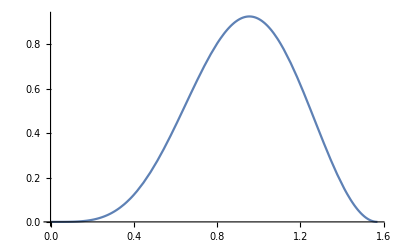

```mathematica
Plot[(g[0,p]/.4)^2,{p,0,Pi/2}]
```

```mathematica
dt=D[f[t,p],t]
dp=D[f[t,p],p]
```

{-Sin[p] Sin[t],Cos[t] Sin[p],0}

{Cos[p] Cos[t],Cos[p] Sin[t],-Sin[p]}

```mathematica
v=Cross[dp,dt];
Norm[v]
```

√(Cos[t]^2 Sin[p]^4+Sin[p]^4 Sin[t]^2+(Cos[p] Cos[t]^2 Sin[p]+Cos[p] Sin[p] Sin[t]^2)^2)

```mathematica
g[x_,y_,z_]=(x^2+y^2)z;
Apply[g, f[t,p]]
```

Cos[p] (Cos[t]^2 Sin[p]^2+Sin[p]^2 Sin[t]^2)

```mathematica
integrand=Simplify[Apply[g,f[t,p]]*Norm[Cross[dp,dt]]]
Integrate[integrand,{p,0,Pi/2},{t,0,2Pi}]
```

Cos[p] (Sin[p]^2)^(3/2)

π/2

```mathematica
mass1=Integrate[integrand,{p,0,Pi/6},{t,0,2Pi}]
mass2=Integrate[integrand,{p,Pi/6,2Pi/6},{t,0,2Pi}]
mass3=Integrate[integrand,{p,2Pi/6,3Pi/6},{t,0,2Pi}]
```

π/32

π/4

(7 π)/32

```mathematica
area1=Integrate[Norm[Cross[dp,dt]],{p,0,Pi/6},{t,0,2Pi}]
area2=Integrate[Norm[Cross[dp,dt]],{p,Pi/6,2Pi/6},{t,0,2Pi}]
area3=Integrate[Norm[Cross[dp,dt]],{p,2Pi/6,3Pi/6},{t,0,2Pi}]
```

-((-2+√3) π)

(-1+√3) π

π

```mathematica
avgdens1=N[mass1/area1]
avgdens2=N[mass2/area2]
avgdens3=N[mass3/area3]
```

0.116627

0.341506

0.21875

```mathematica
ShowTorus[3,1]
```

-Graphics3D-

```mathematica
f[p_,t_]={(Cos[t]+3)Cos[p],(Cos[t]+3)Sin[p],Sin[t]};
```

```mathematica
ParametricPlot3D[f[p,t],{p,0,2 π},{t,0,π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[f[p,t],{p,0,2Pi},{t,0,Pi},ColorFunction->Function[{x,y,z,t},GrayLevel[(1-z)]]]
```

-Graphics3D-

```mathematica
g[x_,y_,z_]=z+1 ;
```

```mathematica
dp=D[f[p,t],p];
dt=D[f[p,t],t];
```

```mathematica
integrand=Simplify[Apply[g,f[p,t]]]*Norm[Cross[dp,dt]];
ans=Integrate[integrand,{p,0,2Pi},{t,0,Pi}];
Simplify[ans]
N[ans]
```

6 π (2+π)

96.9167

***** Exercise 1 start*****

```mathematica
f[s_,t_]={t Cos[2Pi t], t Sin[2Pi t], s *(4-t)}
ParametricPlot3D[f[s,t],{s,0,1},{t,0,4},PlotPoints->{5,200}]
```

{t Cos[2 π t],t Sin[2 π t],s (4-t)}

-Graphics3D-

```mathematica
ds=D[f[s,t],s]
dt=D[f[s,t],t]
```

{0,0,4-t}

{Cos[2 π t]-2 π t Sin[2 π t],2 π t Cos[2 π t]+Sin[2 π t],-s}

```mathematica
integrand=Norm[Cross[ds,dt]]
```

√((-8 π t Cos[2 π t]+2 π t^2 Cos[2 π t]-4 Sin[2 π t]+t Sin[2 π t])^2+(4 Cos[2 π t]-t Cos[2 π t]-8 π t Sin[2 π t]+2 π t^2 Sin[2 π t])^2)

```mathematica
area=Integrate[integrand,{s,0,1},{t,0,4}]
```

8 √(1+64 π^2)-(-1+(1+64 π^2)^(3/2))/(12 π^2)+ArcSinh[8 π]/π

```mathematica
Simplify[area]
```

8 √(1+64 π^2)-(-1+(1+64 π^2)^(3/2))/(12 π^2)+ArcSinh[8 π]/π

```mathematica
N[area]
```

68.1168

*****End of exercise 1*********

*****start of exercise 4*********

Evaluate the surface integral of the function g(x,y,z)=x^2+y^2 over the following surface:


You should include a picture of the surface along with your work.  As with exercises 2 and 3, you’ll have to use NIntegrate here.

```mathematica
g[x_,y_, z_]={x^2+y^2}
```

{x^2+y^2}

```mathematica
f[p_,t_]={Sin[p]Cos[t],Sin[p]Sin[t],Cos[p](1+Cos[3t]/4)}
ParametricPlot3D[f[p,t],{p,Pi/4,3Pi/4},{t,0,2Pi}]
```

{Cos[t] Sin[p],Sin[p] Sin[t],Cos[p] (1+1/4 Cos[3 t])}

-Graphics3D-

```mathematica
dp=D[f[p,t],p]
dt=D[f[p,t],t]
```

{Cos[p] Cos[t],Cos[p] Sin[t],-((1+1/4 Cos[3 t]) Sin[p])}

{-Sin[s] Sin[t],Cos[t] Sin[s],-3/4 Cos[s] Sin[3 t]}

```mathematica
integrand=Simplify[Apply[g,f[p,t]]]*Norm[Cross[dp,dt]]
```

{Sin[p]^2 √((-3 Cos[t] Sin[p] Sin[s]-Cos[t]^2 Sin[p] Sin[s]+3 Cos[p] Sin[s] Sin[t]+Cos[p] Cos[t] Sin[s] Sin[t])^2+(-9/4 Cos[p] Cos[s] Sin[3 t]-3/4 Cos[p] Cos[s] Cos[t] Sin[3 t])^2+(-9/4 Cos[s] Sin[p] Sin[3 t]-3/4 Cos[s] Cos[t] Sin[p] Sin[3 t])^2)}

```mathematica
surf_int=Integrate[integrand,{p,Pi/4,3Pi/4},{t,0,2Pi}]
```

```mathematica
Simplify[surf_int]
```

```mathematica
N[surf_int]
```

*****End of exercise 4*********